```mathematica
v[a_,m_,n_]:=a^2+m a^3+n a^4
```

```mathematica
vv[a_]:=v[a+1,-1,1/4]
```

```mathematica
vpp[a_]=D[vv[a],{a,2}]
```

2-6 (1+a)+3 (1+a)^2

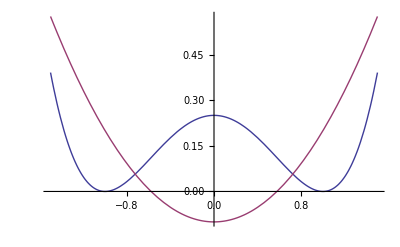

```mathematica
Plot[{vv[a],vpp[a]/10},{a,-1.5,1.5}]
```